```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

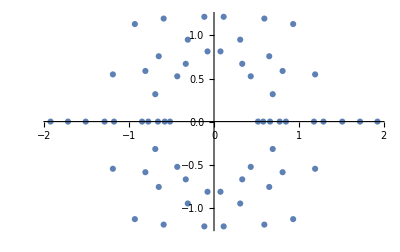

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
fastRootCalculate[n_Integer,x_:Unique[]]:=With[{
poly=1+#+Tuples[{1,-1},n-1]. #^Range[2,n]&,
solve=If[$VersionNumber<12.3,x/.NSolve@##&,NSolveValues],
mirror=If[n>3,Thread,Identity]@Join[#,-#]&,
map=If[n>5,ParallelMap,Map],
k=2$ProcessorCount-$KernelCount},
If[k>0&&n>5,LaunchKernels@k];
map[solve[#==0,x]&,poly@x]//mirror]
```

```mathematica
Block[{r,k=2$ProcessorCount-$KernelCount},
If[k>0,LaunchKernels@k];AbsoluteTiming[r=fastRootCalculate[10];]]
```

{0.444503,Null}

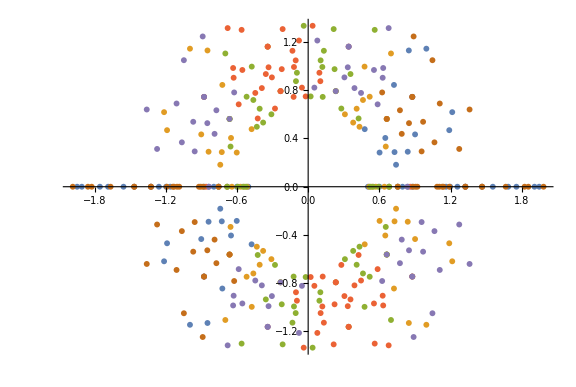

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
displayRoots[n_]:=With[{
p=fastRootCalculate[n],
r=PlotRange->4.1{#,#}2^-{1,3/2}&[{-1,1}],
o=Total@Range[14-n]+3Clip[8.2-n/2]/2+5/2,
m=If[n<6,40/(n+7),1]},
With[{
g={#2[[#]],Hue[#/n],Point@ReIm@p[[#]]}&,
s=AbsolutePointSize/@Table[o/m,n]~Riffle~If[n==18,2,o/m],
a=AspectRatio->Tr@Ratios[Differences/@Last@r],
l=PlotLabel->Style[Row@{"n = ",n},FontSize->120/m],
w=ImageSize->5000/m},
If[m==1,
Graphics[Flatten[g[#,s]&~Array~n],w,r,l],
ComplexListPlot[p,PlotStyle->Last@s,a,w,r,l]~Magnify~m]]
]
```

```mathematica
Block[{r},AbsoluteTiming[r=fastRootCalculate@18;]]
```

{139.917,Null}

```mathematica
Block[{g,a=AbsoluteTiming,t={0,0,0},k},
k=2 $ProcessorCount-$KernelCount;
If[k>0,LaunchKernels@k];k="1.png";
Print["Calculating roots: n = 1."];
t=First/@{
a[g=displayRoots[1];Print["Rendering: "<>k];],
a[g=Rasterize[g,"Image",Background->None];],
a[Export[k,g];g=1;DeleteFile[k];]};
Column@Prepend[{t},"Timing Values (sec):"]]
```

Timing Values (sec):
{0.0886377,2.99419,1.45698}

```mathematica
Block[{t=Table[{0,0},20],g="r-output",a=AbsoluteTiming,f},
f=2$ProcessorCount-$KernelCount;
If[f>0,LaunchKernels@f;Pause@1];
CreateDirectory[g]//Quiet;
f=Array[FileNameJoin[{g,ToString@#<>".png"}]&,Length@t];
Do[Print[Row@{"Calculating roots: n = ",i}~Style~Red];
t[[i]]=First/@{
a[g=displayRoots[i];Print["Rendering: "<>f[[i]]];],
a[Export[f[[i]],g,Background->None];]},
{i,Length@t}];
g={n,"Calculations","Graphics & Saving"};
Print["Done!"];CloseKernels[];
a=First/@{
a[CreateArchive[f,"littlewood.zip",OverwriteTarget->True];],
a[f=Import/@f;],
a[Export["littlewood.gif",f,"DisplayDurations"->3/2];]};
f={"Create Archive","Import Files","Make gif"};
Column@Riffle[" "~Table~4,{
Style["Timing Values (sec):",FontSize->14,FontWeight->Bold],
TableForm[MapIndexed[#2~Join~#1&,t],TableHeadings->{None,g}],
Style["Finalize & publish the results:",FontSize->14],
TableForm[{a},TableHeadings->{None,f}]}]
]
```

$Aborted